```mathematica
wavelengthCylindricalInterferometer=658.0   *10^-9 (*Multiply by interferometer wavelength,units:data *);
```

## initial Scratch

#### convert to zygo format

```mathematica
(*
convertNASAcylindricalDataToZygoXYZ[
(* fileName_ *)"E:\\ScanDataFiles\\NASAcylindricalWavefrontInterferometer\\20231108 - HighRi - Phase II - Sample 1\\20231108-1130-HighRi-P2-Sample1-ROC34mm-Mask20mm-12.h5",
(* maskXstart_ *)maskXstartSample1 ,
(* maskXend_ *)maskXendSample1 ,
(* maskYstart_ *)maskYstartSample1,
(* maskYend_ *)maskYendSample1,
(* pixelSizeInNanometers_ *)31250
]
*)
```

#### reading a file

```mathematica
aDatasetQQ=Import[ToString["E:\\ScanDataFiles\\NASAcylindricalWavefrontInterferometer\\20231108 - HighRi - Phase II - Sample 2\\20231108-1057-HighRi-P2-Sample2-ROC77mm-Mask25mm-8.h5"],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}];
```

```mathematica
dimensionsOfImageArrayData[
aDatasetQQ
]
```

{982,1003}

```mathematica
Image[
normalizeAmplitudeOf2Darray[
aDatasetQQ
]
]
```

-Graphics-

### sub - aperture (full)

```mathematica
maskXstartSample2 = 685;
maskXendSample2 = 965;
maskYstartSample2 = 505;
maskYendSample2= 775

Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
aDatasetQQ,
(* maskXstart_ *)maskXstartSample2 ,
(* maskXend_ *)maskXendSample2 ,
(* maskYstart_ *)maskYstartSample2,
(* maskYend_ *)maskYendSample2
]
]
]
```

775

Part::take: Cannot take positions 505 through 775 in aDatasetQQ.

Part::take: Cannot take positions 685 through 965 in aDatasetQQ.

Part::take: Cannot take positions 685 through 965 in 505;;775.

General::stop: Further output of Part::take will be suppressed during this calculation.

Image::imgarray: The specified argument {(-Min[aDatasetQQ⟦685;;965⟧,(505;;775)⟦685;;965⟧]+aDatasetQQ⟦685;;965⟧)/(Max[aDatasetQQ⟦685;;965⟧,(505;;775)⟦685;;965⟧]-Min[aDatasetQQ⟦Span[«2»]⟧,Span[«2»]⟦Span[«2»]⟧]),(-Min[aDatasetQQ⟦685;;965⟧,(505;;775)⟦685;;965⟧]+(505;;775)⟦685;;965⟧)/(Max[aDatasetQQ⟦685;;965⟧,(505;;775)⟦685;;965⟧]-Min[aDatasetQQ⟦Span[«2»]⟧,Span[«2»]⟦Span[«2»]⟧])} should be an array of rank 2 or 3 with machine-sized numbers.

Image[{(-Min[aDatasetQQ⟦685;;965⟧,(505;;775)⟦685;;965⟧]+aDatasetQQ⟦685;;965⟧)/(Max[aDatasetQQ⟦685;;965⟧,(505;;775)⟦685;;965⟧]-Min[aDatasetQQ⟦685;;965⟧,(505;;775)⟦685;;965⟧]),(-Min[aDatasetQQ⟦685;;965⟧,(505;;775)⟦685;;965⟧]+(505;;775)⟦685;;965⟧)/(Max[aDatasetQQ⟦685;;965⟧,(505;;775)⟦685;;965⟧]-Min[aDatasetQQ⟦685;;965⟧,(505;;775)⟦685;;965⟧])}]

### sub - aperture (partial)

#### quick look

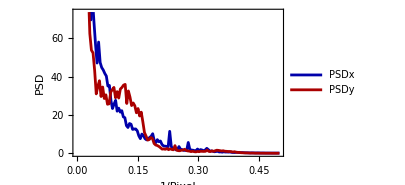
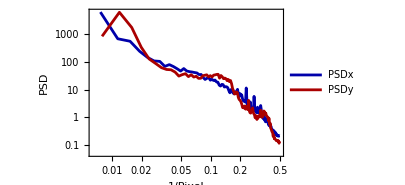
(RMS :   
105.309
Peak to Valley : 
751.
{ Min ,  Max } :
{129.,880.}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
103.365
-Graphics-
-Graphics-)

```mathematica
quickLookAtImageData[
maskImageDataToPoints[
aDatasetQQ,
 maskXstart = maskXstartSample2 +10,
 maskXend =maskXendSample2 -10,
maskYstart = maskYstartSample2+10,
maskYend =maskYendSample2-10
]
]//MatrixForm
```

#### reviewing all files in the directory

```mathematica
Table[
Image[
normalizeAmplitudeOf2Darray[
wavelengthCylindricalInterferometer*Import[ToString[fileName],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}]
]
],
{fileName,sample2files}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### honing in on a workable area within the full recorded data in the FOV

```mathematica
analysisMaskSpan = 250;

maskXstartSample2process = 690;
maskXendSample2process = maskXstartSample2process + analysisMaskSpan;
maskYstartSample2process = 510;
maskYendSample2process= maskYstartSample2process + analysisMaskSpan;

Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
aDatasetQQ,
(* maskXstart_ *)maskXstartSample2process ,
(* maskXend_ *)maskXendSample2process,
(* maskYstart_ *)maskYstartSample2process ,
(* maskYend_ *)maskYendSample2process
]
]
]
```

-Graphics-

```mathematica
Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[sample2files[[1]]],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
(* maskXstart_ *)maskXstartSample2process-45 ,
(* maskXend_ *)maskXstartSample2process-45+analysisMaskSpan,
(* maskYstart_ *)maskYstartSample2process-5 ,
(* maskYend_ *)maskYendSample2process-5
]
]
]
```

-Graphics-

### masking all the datasets to the same size

```mathematica
xStarts = Join[{maskXstartSample2process-45 ,maskXstartSample2process-45},Table[maskXstartSample2process, {nn,1,Length[sample2files]-2}]]
yStarts = Join[{maskYstartSample2process-5 ,maskYstartSample2process-5},Table[maskYstartSample2process, {nn,1,Length[sample2files]-2}]]
```

{645,645,690,690,690,690,690,690,690,690,690,690,690,690}

{505,505,510,510,510,510,510,510,510,510,510,510,510,510}

```mathematica
sample2regionsForProcessing = Table[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[sample2files[[nn]]],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
xStarts[[nn]],
 xStarts[[nn]] +analysisMaskSpan,
yStarts[[nn]] ,
yStarts[[nn]] +analysisMaskSpan
],
{nn,1,Length[sample2files]}
];
```

```mathematica
Table[
Image[
normalizeAmplitudeOf2Darray[
sample2regionsForProcessing[[nn]]
]
],
{nn, 1,Length[sample2files]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sample2QuickLook =Table[
quickLookAtImageData[
sample2regionsForProcessing[[nn]] 
],
{nn,1,Length[sample2files]}
];
```

```mathematica
sample2psdPlotsQuickLook = Table[
sample2QuickLook[[nn]][[-1]],
{nn,1,Length[sample2files]}
];
```

```mathematica
sample2psdPlotsQuickLook
```

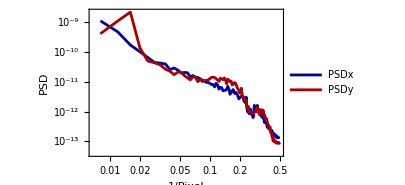
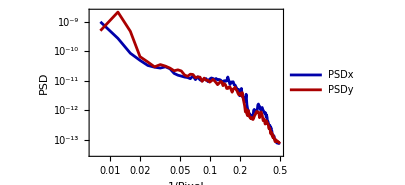
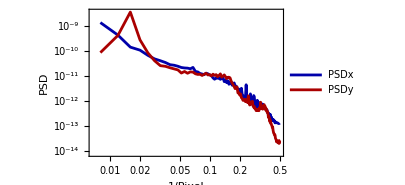
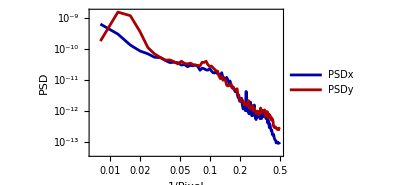
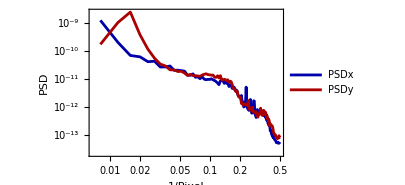
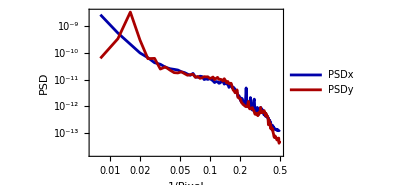
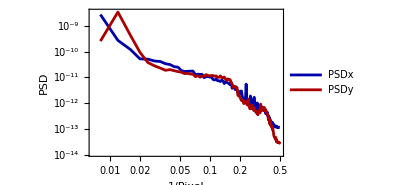
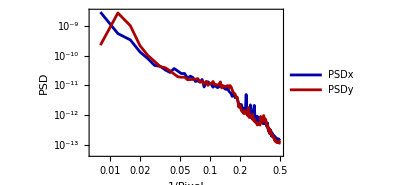

```mathematica
31.250*250
```

7812.5

## Inspection 20231108 - HighRi - Phase II - Sample 2

#### Defining coordinates of mask, and pointing to directory

```mathematica
maskXstart = maskXstartSample2+10;
 maskXend =maskXendSample2-10;
maskYstart = maskYstartSample2+10;
maskYend =maskYendSample2-10;
```

```mathematica
sample2files = FileNames["E:\\ScanDataFiles\\NASAcylindricalWavefrontInterferometer\\20231108 - HighRi - Phase II - Sample 2\\*.h5"
];
```

```mathematica
maskXspan = maskXend-maskXstart
maskYspan = maskYend - maskYstart
```

260

250

#### loading to memory

```mathematica
lookAtSubApSample2=Table[
quickLookAtImageData[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[fileName],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstart,
 maskXend ,
maskYstart,
maskYend 
]
]//MatrixForm,
{fileName,sample2files}];
```

```mathematica
quickLookAtImageData[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[fileName],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstart,
 maskXend ,
maskYstart,
maskYend 
]
]
```

```mathematica
Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[sample2files [[2]]],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstart-55,
maskXstart-55+maskXspan,
maskYstart-15,
maskYstart-15+maskYspan
]
]
]
```

-Graphics-

#### first two are at different detector region below is a different masked area (same dimensions)

```mathematica
firstSample2 =quickLookAtImageData[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[sample2files [[1]]],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstart-55,
maskXstart-55+maskXspan,
maskYstart-15,
maskYstart-15+maskYspan
]
]//MatrixForm;
```

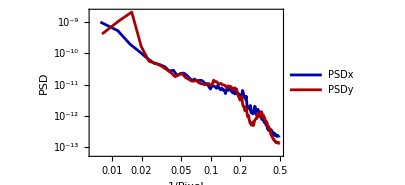
(-Graphics-
-Graphics-)

```mathematica
{firstSample2[[-1]][[-5]],
firstSample2[[-1]][[-1]]}//MatrixForm
```

```mathematica
secondSample2 =quickLookAtImageData[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[sample2files [[2]]],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
maskXstart-55,
maskXstart-55+maskXspan,
maskYstart-15,
maskYstart-15+maskYspan
]
]//MatrixForm;
```

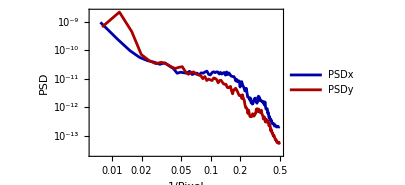
(-Graphics-
-Graphics-)

```mathematica
{secondSample2[[-1]][[-5]],
secondSample2[[-1]][[-1]]}//MatrixForm
```

#### summary

```mathematica
summaryOutputSubApSample2 = Table[
{lookAtSubApSample2[[nn]][[-1]][[-5]],
lookAtSubApSample2[[nn]][[-1]][[-1]]}//MatrixForm,
{nn,1,Length[lookAtSubApSample2]}]
```

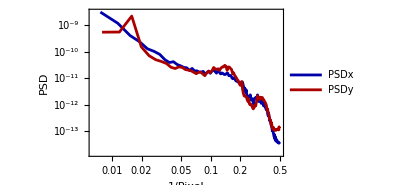
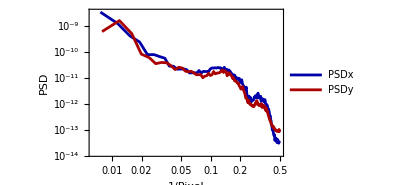
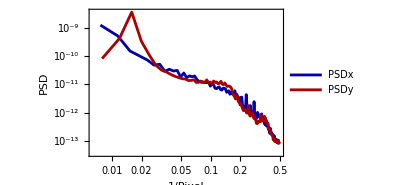
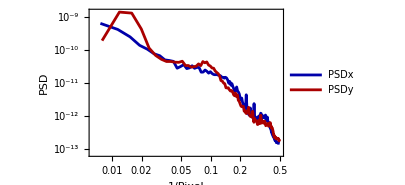
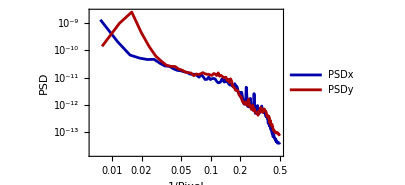
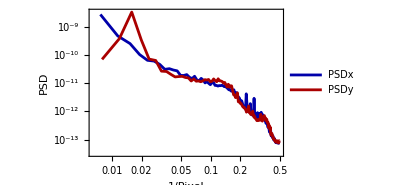
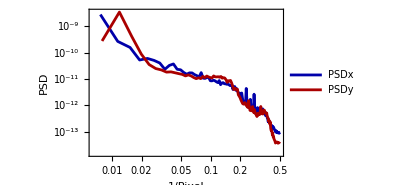
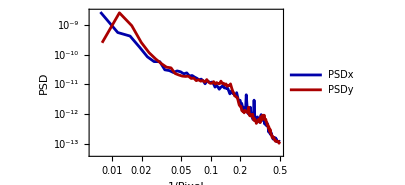
```mathematica
{({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}})
,({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}}),({{-Graphics-}, {-Graphics-}})}
```

#### quickLookAtImageData

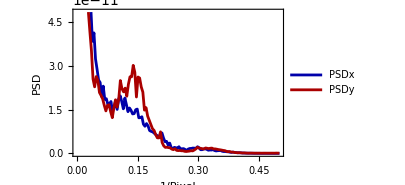
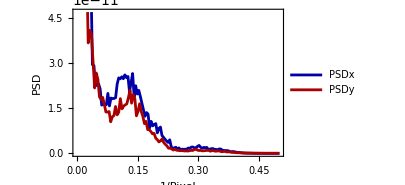
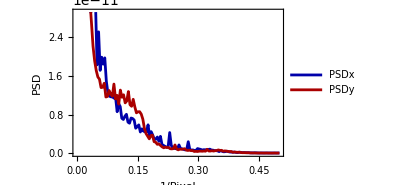
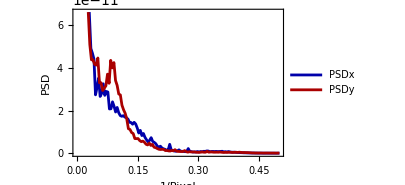
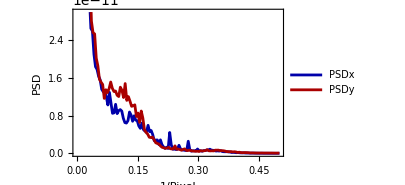
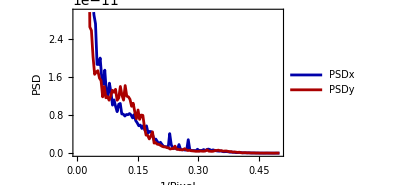
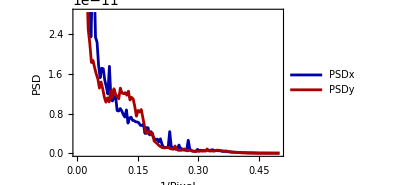
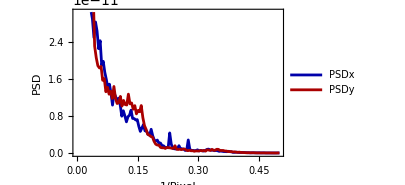
{(RMS :   
0.000108455
Peak to Valley : 
0.000617862
{ Min ,  Max } :
{0.000055272,0.000673134}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.000088414
-Graphics-
-Graphics-),(RMS :   
0.000107026
Peak to Valley : 
0.000622468
{ Min ,  Max } :
{0.000050666,0.000673134}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000899746
-Graphics-
-Graphics-),(RMS :   
0.0000723107
Peak to Valley : 
0.000480998
{ Min ,  Max } :
{0.00008225,0.000563248}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000715647
-Graphics-
-Graphics-),(RMS :   
0.0000675898
Peak to Valley : 
0.00059549
{ Min ,  Max } :
{0.000077644,0.000673134}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000667727
-Graphics-
-Graphics-),(RMS :   
0.0000691873
Peak to Valley : 
0.000546798
{ Min ,  Max } :
{0.0000658,0.000612598}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000691369
-Graphics-
-Graphics-),(RMS :   
0.0000690769
Peak to Valley : 
0.000534954
{ Min ,  Max } :
{0.000086198,0.000621152}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000689148
-Graphics-
-Graphics-),(RMS :   
0.0000696021
Peak to Valley : 
0.00050008
{ Min ,  Max } :
{0.000080934,0.000581014}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000690112
-Graphics-
-Graphics-),(RMS :   
0.0000706536
Peak to Valley : 
0.000499422
{ Min ,  Max } :
{0.000077644,0.000577066}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.000069932
-Graphics-
-Graphics-),(RMS :   
0.0000695228
Peak to Valley : 
0.000512582
{ Min ,  Max } :
{0.00008883,0.000601412}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000689596
-Graphics-
-Graphics-),(RMS :   
0.0000692936
Peak to Valley : 
0.000494158
{ Min ,  Max } :
{0.000084882,0.00057904}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000680144
-Graphics-
-Graphics-),(RMS :   
0.0000683135
Peak to Valley : 
0.000527058
{ Min ,  Max } :
{0.000069748,0.000596806}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.000068269
-Graphics-
-Graphics-),(RMS :   
0.0000685164
Peak to Valley : 
0.00058891
{ Min ,  Max } :
{0.000084224,0.000673134}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000682576
-Graphics-
-Graphics-),(RMS :   
0.0000677493
Peak to Valley : 
0.00047376
{ Min ,  Max } :
{0.000083566,0.000557326}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000667562
-Graphics-
-Graphics-),(RMS :   
0.0000660249
Peak to Valley : 
0.000494158
{ Min ,  Max } :
{0.000075012,0.00056917}
{ numXcoords , numYcoords }  : 
{261,251}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000634406
-Graphics-
-Graphics-)}

```mathematica
lookAtSubApSample2
```